## Calculation of M iteratively - Exact sol.

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}}, endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-60==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];

cM = Compile[{{p,_Real}, {μ,_Real},{ϕp,_Real}},
endϕ = cend[p,μ];
iniϕ = cini[p,μ];
deltaR =  2.1 10^-9;
M=  (-(12 deltaR p^2 π^2 (ϕp/μ)^(2 p))/(ϕp^2 (-1+(ϕp/μ)^p)^3))^(1/4)];
```

```mathematica
(*For values of μ in the range 1 <  μ < 5, the time of integration must be near to 10^8 and for higher values of μ is close to 10^6*)
```

```mathematica
cϕeval = Compile[{{p,_Real}, {μ,_Real},{ϕp,_Real}}, 
ϕini = cini[p,μ];
M = cM[p,μ,ϕp];
V[p,t]= M^4(1 - (ϕs[t]/μ)^p);
Vp[p,t] = D[V[p,t],ϕs[t]];
sol = NDSolve[{ϕs'[t]== - Vp[p,t] as[t]/(3as'[t]) ,as'[t] ==as[t] √(1/3 V[p,t]), ϕs[0] ==ϕini[[1]], as[0] == 1},{ϕs,as}, {t,0, 4.06 10^8}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];
Vt[t_]= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,4.06 10^8}];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];

teval[k_]=  FindRoot[k==pa[t],{t,10^8}];
Print[teval[0.05]];
ϕ[teval[0.05][[1,2]]]];
```

```mathematica
(*At this point you can change the parameters p and μ:*)
```

```mathematica
p =4;
μ = 1;
ϕeval[ϕh_]:= cϕeval[p,μ,ϕh]
```

```mathematica
(*At this point you select the first attempt of ϕ^*, considering that there is some limit to reach convergence, and the number of iterations of the result that you want:*)
```

```mathematica
attemp = cini[p,μ];
iterations = 10;
his = NestList[ϕeval,attemp, iterations]
```

CompiledFunction::cfsa: Argument {0.0455142} at position 3 should be a machine-size real number.

FindRoot::nlnum: The function value {-0.00564681+k} is not a list of numbers with dimensions {1} at {t} = {1.×10^8}.

{t→1.20084×10^8}

NDSolve::mxst: Maximum number of 1782550 steps reached at the point t == 4.02033×10^8.

FindRoot::nlnum: The function value {-0.918085+k} is not a list of numbers with dimensions {1} at {t} = {1.×10^8}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

{t→8.13311×10^7}

{t→8.23266×10^7}

{t→8.22955×10^7}

{t→8.22965×10^7}

{t→8.22965×10^7}

{t→8.22965×10^7}

«3 more identical outputs»

{{0.0455142},0.0513435,0.0511509,0.0511568,0.0511566,0.0511566,0.0511566,0.0511566,0.0511566,0.0511566,0.0511566}

```mathematica
Mvalue[ϕh_]:= cM[p,μ,ϕh]
Mvalue[his[[-1]]]
```

0.000516786

```mathematica
cini[4,μ]
cend[4,μ]
```

{3.44812}

{8.36813}

## Along μ - N = 60 - k = 0.05

```mathematica
p = 4;
Mexact= Compile[{{μ,_Integer}},
attemp = cini[p,μ];
his = NestList[cϕeval[p,μ,#]&,attemp, 10];
 cM[p,μ,his[[-1]]]];
```

```mathematica
listM = Parallelize[Table[{i, Mexact[i]},{i,10,100}]];
```

FindRoot::nlnum: The function value {-1.18972×10^6+k} is not a list of numbers with dimensions {1} at {t} = {1.×10^6}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

CompiledFunction::cfsa: Argument {3.87275} at position 3 should be a machine-size real number.

InterpolatingFunction::dmval: Input value {2.00556×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.10056×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.62736×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression 1.02624×10^-8+1.02624×10^-8 ⅈ should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 4; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression 1.02695×10^-8+1.02695×10^-8 ⅈ should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 4; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression 1.02695×10^-8+1.02695×10^-8 ⅈ should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 4; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

CompiledFunction::cfsa: Argument {4.5638} at position 3 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

```mathematica
(*For this you have to change the time of integration to the order of 10^8*)
```

```mathematica
listM0 = Parallelize[Table[{i, Mexact[i]},{i,4,9}]];
```

FindRoot::nlnum: The function value {-2.19387×10^13+k} is not a list of numbers with dimensions {1} at {t} = {6.×10^6}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

CompiledFunction::cfsa: Argument {0.706452} at position 3 should be a machine-size real number.

InterpolatingFunction::dmval: Input value {6.81856×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.59332×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.57322×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

CompiledFunction::cfsa: Argument {1.08556} at position 3 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

```mathematica
listM = Union[{{1,0.0005167856394252862}, {2,0.001000827942960649 }, {3,0.0014580208022664813}},listM]
```

{{1,0.000516786},{2,0.00100083},{3,0.00145802},{4,0.00188506},{5,0.00227959},{6,0.00264098},{7,0.00297003},{8,0.00326864},{9,0.0035393},{10,0.00378473},{11,0.00400772},{12,0.00421085},{13,0.00439654},{14,0.00456691},{15,0.00472386},{16,0.00486901},{17,0.00500379},{18,0.00512942},{19,0.00524695},{20,0.00535731},{21,0.00546126},{22,0.00555949},{23,0.00565259},{24,0.00574106},{25,0.00582535},{26,0.00590585},{27,0.0059829},{28,0.00605679},{29,0.00612781},{30,0.00619616},{31,0.00626208},{32,0.00632574},{33,0.0063873},{34,0.00644693},{35,0.00650474},{36,0.00656087},{37,0.00661541},{38,0.00666848},{39,0.00672016},{40,0.00677053},{41,0.00681966},{42,0.00686764},{43,0.00691451},{44,0.00696034},{45,0.00700518},{46,0.00704908},{47,0.00709209},{48,0.00713425},{49,0.0071756},{50,0.00721617},{51,0.00725599},{52,0.00729511},{53,0.00733355},{54,0.00737134},{55,0.0074085},{56,0.00744506},{57,0.00748104},{58,0.00751646},{59,0.00755135},{60,0.00758572},{61,0.00761959},{62,0.00765298},{63,0.00768591},{64,0.00771838},{65,0.00775042},{66,0.00778204},{67,0.00781325},{68,0.00784407},{69,0.0078745},{70,0.00790456},{71,0.00793425},{72,0.0079636},{73,0.00799261},{74,0.00802128},{75,0.00804963},{76,0.00807767},{77,0.0081054},{78,0.00813283},{79,0.00815997},{80,0.00818683},{81,0.00821342},{82,0.00823973},{83,0.00826578},{84,0.00829158},{85,0.00831713},{86,0.00834243},{87,0.00836749},{88,0.00839232},{89,0.00841692},{90,0.00844129},{91,0.00846545},{92,0.00848939},{93,0.00851313},{94,0.00853666},{95,0.00855999},{96,0.00858312},{97,0.00860606},{98,0.00862881},{99,0.00865137},{100,0.00867375}}

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv",listM];
```

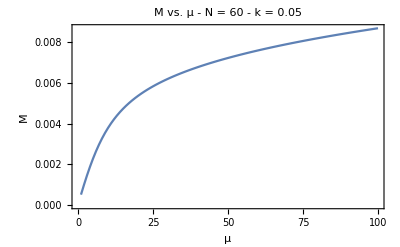

```mathematica
plotM = ListPlot[listM,Joined->True,Frame->True,FrameLabel->{"μ", "M"},PlotLabel->"M vs. μ - N = 60 - k = 0.05"]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Images_observables_ex\\m_vs_mu_k005_N60.png",plotM];
```

## Along μ - N = 50 - k = 0.05

```mathematica
p = 4;
Mexact= Compile[{{μ,_Integer}},
attemp = cini[p,μ];
his = NestList[cϕeval[p,μ,#]&,attemp, 10];
 cM[p,μ,his[[-1]]]];
```

```mathematica
listM = Parallelize[Table[{i, Mexact[i]},{i,8,100}]];
```

FindRoot::nlnum: The function value {(-0.00261205-2.75341×10^-8 ⅈ)+k} is not a list of numbers with dimensions {1} at {t} = {1.×10^6}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

CompiledFunction::cfsa: Argument {2.80163} at position 3 should be a machine-size real number.

InterpolatingFunction::dmval: Input value {3.2431×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.22431×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.00598×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{t→1.70588×10^6}

CompiledFunction::cfse: Compiled expression 0.000032552+0.000032552 ⅈ should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 4; proceeding with uncompiled evaluation.

{t→1.×10^6}

CompiledFunction::cfse: Compiled expression 2.80163+0.0000264758 ⅈ should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 24; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression 0.000032552+0.000032552 ⅈ should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 4; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

{t→1.×10^6}

CompiledFunction::cfsa: Argument 2.80163+0.0000264758 ⅈ at position 3 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

```mathematica
listM = {{8,0.003794680996543442},{9,0.00399428752255276},{10,0.004253007662651811},{11,0.004486386117484074},{12,0.004697811657065193},{13,0.00489025489289082},{14,0.005066287683313105},{15,0.005228104124442245},{16,0.0053775697082877405},{17,0.0055162661819398474},{18,0.0056455347100050415},{19,0.0057665114221233426},{20,0.005880164425741483},{21,0.005987318623501648},{22,0.0060886805833470165},{23,0.006184855811061815},{24,0.006276369765598148},{25,0.00636367619485969},{26,0.006447164622278487},{27,0.0065271856908665086},{28,0.006604034760037719},{29,0.006677984326275493},{30,0.006749264161451484},{31,0.006818085098352709},{32,0.006884633727631415},{33,0.0069490709386025515},{34,0.007011547576502721},{35,0.0070721968439485736},{36,0.00713113886355895},{37,0.007188482281341494},{38,0.007244325641162566},{39,0.00729875856678053},{40,0.007351862782008644},{41,0.007403712993308408},{42,0.0074543776565524755},{43,0.0075039196445345355},{44,0.00755239682991486},{45,0.007599862596012755},{46,0.007646366285421966},{47,0.00769195359490675},{48,0.00773666692430969},{49,0.00778054569324491},{50,0.00782362665783405},{51,0.00786594404675869},{52,0.0079075298267895},{53,0.007948413907154513},{54,0.007988624313448012},{55,0.008028187343652689},{56,0.008067127708472439},{57,0.00810546865785583},{58,0.008143232095162123},{59,0.008180438680461975},{60,0.00821710792417329},{61,0.008253258272019708},{62,0.008288907182443713},{63,0.008324071196886903},{64,0.008358766004058125},{65,0.00839300649873526},{66,0.008426806835343298},{67,0.008460180477428695},{68,0.008493140242667329},{69,0.008525698344492882},{70,0.008557866430367359},{71,0.008589655616972999},{72,0.008621076522863499},{73,0.008652139298367029},{74,0.008682853653580671},{75,0.00871322888392062},{76,0.008743273894126335},{77,0.0087729972205863},{78,0.008802407051556738},{79,0.008831511246727361},{80,0.008860317354843342},{81,0.008888832630381606},{82,0.008917064049234015},{83,0.008945018323017648},{84,0.00897270191274484},{85,0.009000121041501623},{86,0.009027281706341551},{87,0.009054189689455842},{88,0.009080850568531116},{89,0.009107269726677221},{90,0.009133452361655333},{91,0.009159403494460164},{92,0.009185127977587035},{93,0.009210630502685927},{94,0.009235915607825614},{95,0.009260987684321192},{96,0.009285850983222987},{97,0.009310509621419242},{98,0.00933496758734529},{99,0.009359228746542513},{100,0.009383296846736845}};
```

```mathematica
(*For this you have to change the time of integration to the order of 10^8*)
```

```mathematica
listM0 = Parallelize[Table[{i, Mexact[i]},{i,4,7}]]
```

InterpolatingFunction::dmval: Input value {1.×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {-4.16852×10^14+k} is not a list of numbers with dimensions {1} at {t} = {1.×10^7}.

InterpolatingFunction::dmval: Input value {1.×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {-4.16852×10^14+k} is not a list of numbers with dimensions {1} at {t} = {1.×10^7}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

CompiledFunction::cfsa: Argument {0.769037} at position 3 should be a machine-size real number.

CompiledFunction::cfsa: Argument {1.17832} at position 3 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

{{4,0.00218756},{5,0.00262903},{6,0.00302756},{7,0.00338555}}

```mathematica
listM = Union[{{1,0.0006119926676267156}, {2,0.0011763116803796521},{3,0.0017026869097955756}},listM]
```

{{1,0.000611993},{2,0.00117631},{3,0.00170269},{4,0.00218756},{5,0.00262903},{6,0.00302756},{7,0.00338555},{8,0.00379468},{9,0.00399429},{10,0.00425301},{11,0.00448639},{12,0.00469781},{13,0.00489025},{14,0.00506629},{15,0.0052281},{16,0.00537757},{17,0.00551627},{18,0.00564553},{19,0.00576651},{20,0.00588016},{21,0.00598732},{22,0.00608868},{23,0.00618486},{24,0.00627637},{25,0.00636368},{26,0.00644716},{27,0.00652719},{28,0.00660403},{29,0.00667798},{30,0.00674926},{31,0.00681809},{32,0.00688463},{33,0.00694907},{34,0.00701155},{35,0.0070722},{36,0.00713114},{37,0.00718848},{38,0.00724433},{39,0.00729876},{40,0.00735186},{41,0.00740371},{42,0.00745438},{43,0.00750392},{44,0.0075524},{45,0.00759986},{46,0.00764637},{47,0.00769195},{48,0.00773667},{49,0.00778055},{50,0.00782363},{51,0.00786594},{52,0.00790753},{53,0.00794841},{54,0.00798862},{55,0.00802819},{56,0.00806713},{57,0.00810547},{58,0.00814323},{59,0.00818044},{60,0.00821711},{61,0.00825326},{62,0.00828891},{63,0.00832407},{64,0.00835877},{65,0.00839301},{66,0.00842681},{67,0.00846018},{68,0.00849314},{69,0.0085257},{70,0.00855787},{71,0.00858966},{72,0.00862108},{73,0.00865214},{74,0.00868285},{75,0.00871323},{76,0.00874327},{77,0.008773},{78,0.00880241},{79,0.00883151},{80,0.00886032},{81,0.00888883},{82,0.00891706},{83,0.00894502},{84,0.0089727},{85,0.00900012},{86,0.00902728},{87,0.00905419},{88,0.00908085},{89,0.00910727},{90,0.00913345},{91,0.0091594},{92,0.00918513},{93,0.00921063},{94,0.00923592},{95,0.00926099},{96,0.00928585},{97,0.00931051},{98,0.00933497},{99,0.00935923},{100,0.0093833}}

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N50.csv",listM];
```

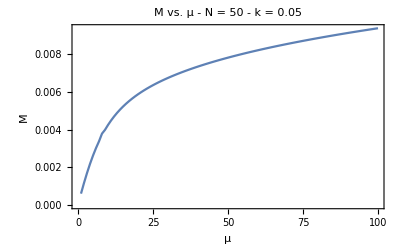

```mathematica
plotM = ListPlot[listM,Joined->True,Frame->True,FrameLabel->{"μ", "M"},PlotLabel->"M vs. μ - N = 50 - k = 0.05"]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Images_observables_ex\\m_vs_mu_k005_N50.png",plotM];
```

## Along μ - N = 60 - k = 0.002

```mathematica
p = 4;
Mexact= Compile[{{μ,_Integer}},
attemp = cini[p,μ];
his = NestList[cϕeval[p,μ,#]&,attemp, 10];
 cM[p,μ,his[[-1]]]];
```

```mathematica
listM = Parallelize[Table[{i, Mexact[i]},{i,7,100}]];
```

```mathematica
(*For this you have to change the time of integration to the order of 10^8*)
```

```mathematica
listM
```

{{9,0.00341862},{10,0.00366004},{11,0.00387985},{12,0.00408044},{13,0.00426406},{14,0.00443272},{15,0.0045882},{16,0.00473208},{17,0.00486573},{18,0.00499032},{19,0.0051069},{20,0.00521635},{21,0.00531943},{22,0.00541682},{23,0.00550909},{24,0.00559676},{25,0.00568026},{26,0.00575998},{27,0.00583625},{28,0.00590937},{29,0.00597961},{30,0.00604721},{31,0.00611237},{32,0.00617528},{33,0.00623609},{34,0.00629497},{35,0.00635205},{36,0.00640744},{37,0.00646125},{38,0.00651359},{39,0.00656455},{40,0.0066142},{41,0.00666263},{42,0.0067099},{43,0.00675607},{44,0.00680121},{45,0.00684536},{46,0.00688858},{47,0.00693091},{48,0.00697239},{49,0.00701307},{50,0.00705298},{51,0.00709215},{52,0.00713062},{53,0.00716841},{54,0.00720555},{55,0.00724208},{56,0.00727801},{57,0.00731337},{58,0.00734817},{59,0.00738244},{60,0.00741621},{61,0.00744947},{62,0.00748227},{63,0.0075146},{64,0.00754648},{65,0.00757794},{66,0.00760898},{67,0.00763962},{68,0.00766986},{69,0.00769973},{70,0.00772923},{71,0.00775837},{72,0.00778716},{73,0.00781562},{74,0.00784375},{75,0.00787156},{76,0.00789906},{77,0.00792627},{78,0.00795317},{79,0.00797979},{80,0.00800613},{81,0.0080322},{82,0.00805801},{83,0.00808355},{84,0.00810885},{85,0.00813389},{86,0.0081587},{87,0.00818327},{88,0.00820761},{89,0.00823172},{90,0.00825562},{91,0.0082793},{92,0.00830277},{93,0.00832603},{94,0.00834909},{95,0.00837195},{96,0.00839462},{97,0.0084171},{98,0.0084394},{99,0.00846151},{100,0.00848344}}

```mathematica
listM0 = Parallelize[Table[{i, Mexact[i]},{i,4,6}]];
```

$Aborted

```mathematica
listM
```

{{9,0.00341862},{10,0.00366004},{11,0.00387985},{12,0.00408044},{13,0.00426406},{14,0.00443272},{15,0.0045882},{16,0.00473208},{17,0.00486573},{18,0.00499032},{19,0.0051069},{20,0.00521635},{21,0.00531943},{22,0.00541682},{23,0.00550909},{24,0.00559676},{25,0.00568026},{26,0.00575998},{27,0.00583625},{28,0.00590937},{29,0.00597961},{30,0.00604721},{31,0.00611237},{32,0.00617528},{33,0.00623609},{34,0.00629497},{35,0.00635205},{36,0.00640744},{37,0.00646125},{38,0.00651359},{39,0.00656455},{40,0.0066142},{41,0.00666263},{42,0.0067099},{43,0.00675607},{44,0.00680121},{45,0.00684536},{46,0.00688858},{47,0.00693091},{48,0.00697239},{49,0.00701307},{50,0.00705298},{51,0.00709215},{52,0.00713062},{53,0.00716841},{54,0.00720555},{55,0.00724208},{56,0.00727801},{57,0.00731337},{58,0.00734817},{59,0.00738244},{60,0.00741621},{61,0.00744947},{62,0.00748227},{63,0.0075146},{64,0.00754648},{65,0.00757794},{66,0.00760898},{67,0.00763962},{68,0.00766986},{69,0.00769973},{70,0.00772923},{71,0.00775837},{72,0.00778716},{73,0.00781562},{74,0.00784375},{75,0.00787156},{76,0.00789906},{77,0.00792627},{78,0.00795317},{79,0.00797979},{80,0.00800613},{81,0.0080322},{82,0.00805801},{83,0.00808355},{84,0.00810885},{85,0.00813389},{86,0.0081587},{87,0.00818327},{88,0.00820761},{89,0.00823172},{90,0.00825562},{91,0.0082793},{92,0.00830277},{93,0.00832603},{94,0.00834909},{95,0.00837195},{96,0.00839462},{97,0.0084171},{98,0.0084394},{99,0.00846151},{100,0.00848344}}

```mathematica
listM = Union[{{1,0.0004930228309617358}, {2,0.0009565686391402293 }, {3,0.00139576225720409},{4, 0.0018074233876812873}, {5, 0.002189187831458298},{6, 0.0025402019956623956}, {7,0.00286099165608357},{8,0.0031530809240629797}},listM]
```

{{1,0.000493023},{2,0.000956569},{3,0.00139576},{4,0.00180742},{5,0.00218919},{6,0.0025402},{7,0.00286099},{8,0.00315308},{9,0.00341862},{10,0.00366004},{11,0.00387985},{12,0.00408044},{13,0.00426406},{14,0.00443272},{15,0.0045882},{16,0.00473208},{17,0.00486573},{18,0.00499032},{19,0.0051069},{20,0.00521635},{21,0.00531943},{22,0.00541682},{23,0.00550909},{24,0.00559676},{25,0.00568026},{26,0.00575998},{27,0.00583625},{28,0.00590937},{29,0.00597961},{30,0.00604721},{31,0.00611237},{32,0.00617528},{33,0.00623609},{34,0.00629497},{35,0.00635205},{36,0.00640744},{37,0.00646125},{38,0.00651359},{39,0.00656455},{40,0.0066142},{41,0.00666263},{42,0.0067099},{43,0.00675607},{44,0.00680121},{45,0.00684536},{46,0.00688858},{47,0.00693091},{48,0.00697239},{49,0.00701307},{50,0.00705298},{51,0.00709215},{52,0.00713062},{53,0.00716841},{54,0.00720555},{55,0.00724208},{56,0.00727801},{57,0.00731337},{58,0.00734817},{59,0.00738244},{60,0.00741621},{61,0.00744947},{62,0.00748227},{63,0.0075146},{64,0.00754648},{65,0.00757794},{66,0.00760898},{67,0.00763962},{68,0.00766986},{69,0.00769973},{70,0.00772923},{71,0.00775837},{72,0.00778716},{73,0.00781562},{74,0.00784375},{75,0.00787156},{76,0.00789906},{77,0.00792627},{78,0.00795317},{79,0.00797979},{80,0.00800613},{81,0.0080322},{82,0.00805801},{83,0.00808355},{84,0.00810885},{85,0.00813389},{86,0.0081587},{87,0.00818327},{88,0.00820761},{89,0.00823172},{90,0.00825562},{91,0.0082793},{92,0.00830277},{93,0.00832603},{94,0.00834909},{95,0.00837195},{96,0.00839462},{97,0.0084171},{98,0.0084394},{99,0.00846151},{100,0.00848344}}

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k0002_N60.csv",listM];
```

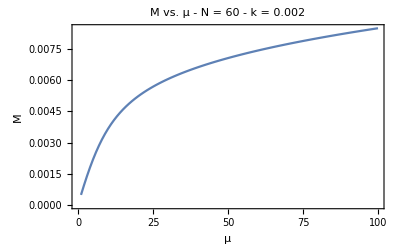

```mathematica
plotM = ListPlot[listM,Joined->True,Frame->True,FrameLabel->{"μ", "M"},PlotLabel->"M vs. μ - N = 60 - k = 0.002"]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Images_observables_ex\\m_vs_mu_k0002_N60.png",plotM];
```

## Along μ - N = 50 - k = 0.002

```mathematica
p = 4;
Mexact= Compile[{{μ,_Integer}},
attemp = cini[p,μ];
his = NestList[cϕeval[p,μ,#]&,attemp, 10];
 cM[p,μ,his[[-1]]]];
```

```mathematica
listM = Parallelize[Table[{i, Mexact[i]},{i,10,100}]];
```

```mathematica
listM
```

{{10,0.00408832},{11,0.00431824},{12,0.0045269},{13,0.00471708},{14,0.0048912},{15,0.00505135},{16,0.00519933},{17,0.00533665},{18,0.00546464},{19,0.0055844},{20,0.00569687},{21,0.00580288},{22,0.00590311},{23,0.00599817},{24,0.00608859},{25,0.0061748},{26,0.00625721},{27,0.00633615},{28,0.00641193},{29,0.00648482},{30,0.00655504},{31,0.00662282},{32,0.00668832},{33,0.00675172},{34,0.00681317},{35,0.0068728},{36,0.00693073},{37,0.00698706},{38,0.00704191},{39,0.00709535},{40,0.00714747},{41,0.00719835},{42,0.00724805},{43,0.00729663},{44,0.00734416},{45,0.00739069},{46,0.00743626},{47,0.00748093},{48,0.00752473},{49,0.0075677},{50,0.00760989},{51,0.00765132},{52,0.00769202},{53,0.00773204},{54,0.00777138},{55,0.00781009},{56,0.00784818},{57,0.00788568},{58,0.00792261},{59,0.007959},{60,0.00799485},{61,0.00803019},{62,0.00806503},{63,0.0080994},{64,0.00813331},{65,0.00816676},{66,0.00819979},{67,0.00823239},{68,0.00826459},{69,0.00829639},{70,0.00832781},{71,0.00835886},{72,0.00838954},{73,0.00841988},{74,0.00844987},{75,0.00847952},{76,0.00850885},{77,0.00853787},{78,0.00856658},{79,0.00859499},{80,0.0086231},{81,0.00865093},{82,0.00867849},{83,0.00870577},{84,0.00873278},{85,0.00875954},{86,0.00878604},{87,0.00881229},{88,0.0088383},{89,0.00886408},{90,0.00888962},{91,0.00891494},{92,0.00894003},{93,0.00896491},{94,0.00898957},{95,0.00901403},{96,0.00903828},{97,0.00906233},{98,0.00908618},{99,0.00910984},{100,0.00913331}}

```mathematica
(*For this you have to change the time of integration to the order of 10^8*)
```

```mathematica
listM = Union[{{1,0.0005775082957896066}, {2,0.0011130797597261944},{3,0.0016149041568326032},{4,0.002079464435222048}, {5,0.002504623372426785}, {6,0.0028903970078603064},{7,0.0032385457927428018},{8,0.003551949444985279},{9,0.003834025811562992}},listM]
```

{{1,0.000577508},{2,0.00111308},{3,0.0016149},{4,0.00207946},{5,0.00250462},{6,0.0028904},{7,0.00323855},{8,0.00355195},{9,0.00383403},{10,0.00408832},{11,0.00431824},{12,0.0045269},{13,0.00471708},{14,0.0048912},{15,0.00505135},{16,0.00519933},{17,0.00533665},{18,0.00546464},{19,0.0055844},{20,0.00569687},{21,0.00580288},{22,0.00590311},{23,0.00599817},{24,0.00608859},{25,0.0061748},{26,0.00625721},{27,0.00633615},{28,0.00641193},{29,0.00648482},{30,0.00655504},{31,0.00662282},{32,0.00668832},{33,0.00675172},{34,0.00681317},{35,0.0068728},{36,0.00693073},{37,0.00698706},{38,0.00704191},{39,0.00709535},{40,0.00714747},{41,0.00719835},{42,0.00724805},{43,0.00729663},{44,0.00734416},{45,0.00739069},{46,0.00743626},{47,0.00748093},{48,0.00752473},{49,0.0075677},{50,0.00760989},{51,0.00765132},{52,0.00769202},{53,0.00773204},{54,0.00777138},{55,0.00781009},{56,0.00784818},{57,0.00788568},{58,0.00792261},{59,0.007959},{60,0.00799485},{61,0.00803019},{62,0.00806503},{63,0.0080994},{64,0.00813331},{65,0.00816676},{66,0.00819979},{67,0.00823239},{68,0.00826459},{69,0.00829639},{70,0.00832781},{71,0.00835886},{72,0.00838954},{73,0.00841988},{74,0.00844987},{75,0.00847952},{76,0.00850885},{77,0.00853787},{78,0.00856658},{79,0.00859499},{80,0.0086231},{81,0.00865093},{82,0.00867849},{83,0.00870577},{84,0.00873278},{85,0.00875954},{86,0.00878604},{87,0.00881229},{88,0.0088383},{89,0.00886408},{90,0.00888962},{91,0.00891494},{92,0.00894003},{93,0.00896491},{94,0.00898957},{95,0.00901403},{96,0.00903828},{97,0.00906233},{98,0.00908618},{99,0.00910984},{100,0.00913331}}

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k0002_N50.csv",listM];
```

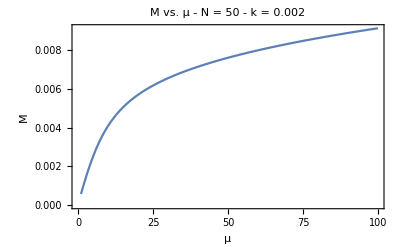

```mathematica
plotM = ListPlot[listM,Joined->True,Frame->True,FrameLabel->{"μ", "M"},PlotLabel->"M vs. μ - N = 50 - k = 0.002"]
```

```mathematica
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Images_observables_ex\\m_vs_mu_k0002_N50.png",plotM];
```